# Differential Cross Section under Frame Transform

```mathematica
mp=938.272;
Lz[β_]:={{1/(√(1-β^2)),0,β/(√(1-β^2))},{0,1,0},{β/(√(1-β^2)),0,1/(√(1-β^2))}};
Momentum[A_]:=√(A[[2]]^2+A[[3]]^2);
KE[A_]:=A[[1]]-√(A[[1]]^2-Momentum[A]^2);
Angle[A_]:=ArcTan[A[[3]],A[[2]]];
(* the Jacobian From CM frame (pC) to Lab frame (pA) *)
Jaco[pC_,β_]:=Module[{pA},pA=Lz[β].pC; (Momentum[pA])^3/(Momentum[pC])^2 (√(1-β^2))/(Momentum[pC]+pC[[1]] β pC[[3]]/Momentum[pC] )]
Jaco2[pC_,β_]:=Module[{pA,θA,θC,γ},
pA=Lz[β].pC;
θC = Angle[pC];
θA= Angle[pA];
γ=1/(√(1-β^2));
 (Momentum[pA])^2/(Momentum[pC])^2 1/( Cos[θA]Cos[θC]+γ Sin[θA]Sin[θC])
]
JacoPOmega[pC_,β_]:=Module[{pA},pA=Lz[β].pC; (Momentum[pA])^2/(Momentum[pC])^2 pC[[1]]/pA[[1]]](* this is double differential X-sec dpdΩ *)
JacoEOmega[pC_,β_]:=Module[{pA},pA=Lz[β].pC; Momentum[pA]/Momentum[pC] pA[[1]]/pC[[1]]]
JacoNonRel[pC_,β_]:=Module[{pA},pA=Lz[β].pC; KE[pA]/KE[pC] 1/Cos[ArcTan[pC[[3]],pC[[2]]]-ArcTan[pA[[3]],pA[[2]]]]]
Manipulate[
Plot[{
Abs[Jaco[{e,p Sin[θ °],p Cos[θ °]},β]],
Abs[Jaco2[{e,p Sin[θ °],p Cos[θ °]},β]],
Abs[JacoNonRel[{e,p Sin[θ °],p Cos[θ °]},β]]
},{θ,0,180},PlotRange->{0,10},Frame-> True, FrameLabel->{"Angle CM[deg]","dΩ_CM/dΩ_Lab"},GridLines-> {Table[10 i,{i,1,18}],Table[i,{i,0, 10, 1}]},GridLinesStyle->Directive[Dotted],ImageSize->500,

PlotStyle->{Red,Blue,Green},PlotLabel->" dσ/dΩ from CM frame to Lab, Mass_eff = "<>ToString[√(e^2-p^2)]<>", β_part = "<>ToString[p/e]],
{{β,0.5,"Transform β"},-1,1, Appearance->"Labeled" },
{{p,√(2 mp 100 + 10000),"Momentum_CM"},0,1000, Appearance->"Labeled" },
{{e,mp+100,"Energy_CM"},0.1,2000, Appearance->"Labeled" }]
```

```mathematica
Manipulate[
ParametricPlot[
{Angle[(Lz[β].{e,p Sin[θ °],p Cos[θ °]})] 180/π,(Lz[β].{e,p Sin[θ °],p Cos[θ °]})[[1]]-mp},
{θ,0,360},Frame-> True,FrameLabel->{"θ_Lab","T_Lab"}, GridLines->Automatic,GridLinesStyle->Directive[Dotted], PlotRange->{{-180,180},{0,1000}},AspectRatio->1
],
{{β,0.5,"Transform β"},-1,1, Appearance->"Labeled" },
{{p,√(2 mp 100 + 10000),"Momentum_CM"},0,1000, Appearance->"Labeled" },
{{e,mp+100,"Energy_CM"},0.1,2000, Appearance->"Labeled" }]
```

```mathematica
Manipulate[
GraphicsGrid[{{
Show[
ParametricPlot[
{{e,p Sin[θ °],p Cos[θ °]}[[{3,2}]],
(Lz[β].{e,p Sin[θ °],p Cos[θ °]})[[{3,2}]]
},
{θ,0,360},Frame-> True, FrameLabel->{"p_z","p_x"},GridLines->Automatic,GridLinesStyle->Directive[Dotted]
],
Graphics[{
{Blue,Arrow[{{0,0}, p{Cos[θt °],Sin[θt °]}}]},
{Red,Arrow[{{0,0},(Lz[β].{e,p Sin[θt °],p Cos[θt °]})[[{3,2}]]}]}
}]
],
ParametricPlot[
{Angle[Lz[β].{e,p Sin[θ °],p Cos[θ °]}]*180/π,Jaco[{e,p Sin[θ °],p Cos[θ °]},β]}
,
{θ,0,180},Frame-> True, FrameLabel->{"Angle Lab [deg]","dΩ_CM/dΩ_Lab"},GridLines->Automatic,GridLinesStyle->Directive[Dotted],AspectRatio->0.6,PlotRange->{{0,70},{-1,7}},
PlotLabel->" dσ/dΩ from CM frame to Lab, Mass_eff = "<>ToString[√(e^2-p^2)]<>", β_part = "<>ToString[p/e]]
}
}
,ImageSize->900],
{{θt,45,"θ"},-180,180},
{{β,0.5,"Transform β"},-1,1, Appearance->"Labeled" },
{{p,√(2 mp 100 + 10000),"Momentum_CM"},0,1000, Appearance->"Labeled" },
{{e,mp+100,"Energy_CM"},0.1,2000, Appearance->"Labeled" }]
```

1.99856

-0.00143852

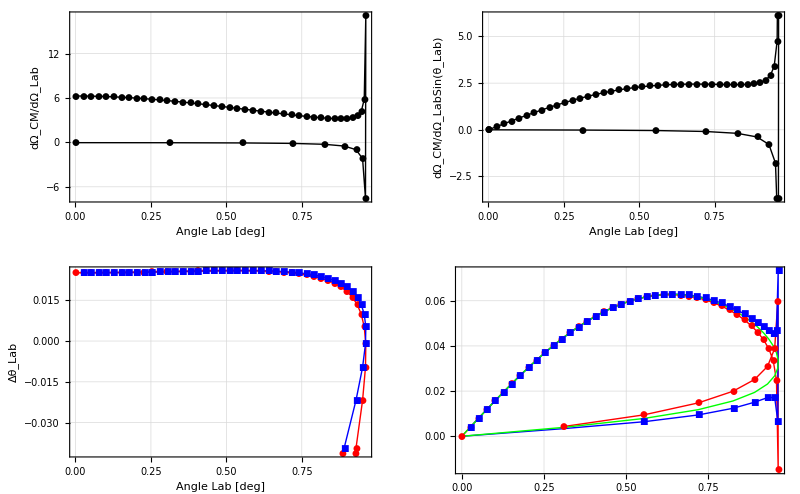

```mathematica
(* check the Integrated cross section *)
testβ=0.5;
CMRange=π;
step=50;
data=Table[{Angle[Lz[testβ].{mp+100,√(2 mp 100 + 10000) Sin[θc ],√(2 mp 100 + 10000) Cos[θc ]}],Jaco2[{mp+100,√(2 mp 100 + 10000) Sin[θc],√(2 mp 100 + 10000) Cos[θc]},testβ]},{θc,0,CMRange,CMRange/step}];
preIntData=Table[
{data[[i,1]],data[[i,2]] Sin[data[[i,1]]]}
,{i,1, Length[data]}];
UpperIntData=Table[
{preIntData[[i,1]],
preIntData[[i+1,1]]-preIntData[[i,1]],
 preIntData[[i,2]]}
,{i,1,Length[preIntData]-1}];
LowerIntData=Table[
{preIntData[[i,1]],
preIntData[[i,1]]-preIntData[[i-1,1]],
 preIntData[[i,2]]}
,{i,2,Length[preIntData]}];

UpperInt=Sum[UpperIntData[[i,2]]*UpperIntData[[i,3]],{i,1,Length[UpperIntData]}];
LowerInt=Sum[LowerIntData[[i,2]]*LowerIntData[[i,3]],{i,1,Length[LowerIntData]}];
Mean[{UpperInt,LowerInt}]
%-NIntegrate[Sin[θc],{θc,0,CMRange}]
GraphicsGrid[{
{ListPlot[data,(*Joined->True,*)Frame->True, FrameLabel->{"Angle Lab [deg]","dΩ_CM/dΩ_Lab"},GridLines->Automatic,GridLinesStyle->Directive[Dotted],PlotStyle->Black,Joined->True,PlotMarkers->Automatic],
ListPlot[preIntData,(*Joined->True,*)Frame->True, FrameLabel->{"Angle Lab [deg]","dΩ_CM/dΩ_LabSin(θ_Lab)"},GridLines->Automatic,GridLinesStyle->Directive[Dotted],PlotStyle->Black,Joined->True,PlotMarkers->Automatic]},
{ListPlot[{
Table[UpperIntData[[i,1;;2]],{i,1,Length[UpperIntData]}],
Table[LowerIntData[[i,1;;2]],{i,1,Length[LowerIntData]}]
},(*Joined->True,*)Frame->True, FrameLabel->{"Angle Lab [deg]","Δθ_Lab"},GridLines->Automatic,GridLinesStyle->Directive[Dotted],PlotStyle->{Red,Blue},Joined->True,PlotMarkers->Automatic],
ListPlot[{
Table[{UpperIntData[[i,1]],UpperIntData[[i,2]]*UpperIntData[[i,3]]},{i,1,Length[UpperIntData]}],
Table[{LowerIntData[[i,1]],LowerIntData[[i,2]]*LowerIntData[[i,3]]},{i,1,Length[LowerIntData]}],
Table[{Angle[Lz[testβ].{mp+100,√(2 mp 100 + 10000) Sin[θc ],√(2 mp 100 + 10000) Cos[θc ]}],Sin[θc] CMRange/step},{θc,0,CMRange,CMRange/step}]
},(*Joined->True,*)Frame->True, FrameLabel->{"Angle Lab [deg]","dΩ_CM/dΩ_LabSin(θ_Lab)Δθ_Lab"},GridLines->Automatic,GridLinesStyle->Directive[Dotted],PlotStyle->{Red,Blue,Green},Joined->True,PlotMarkers->Automatic]}},ImageSize->800]
```

## Compare with PP elastics

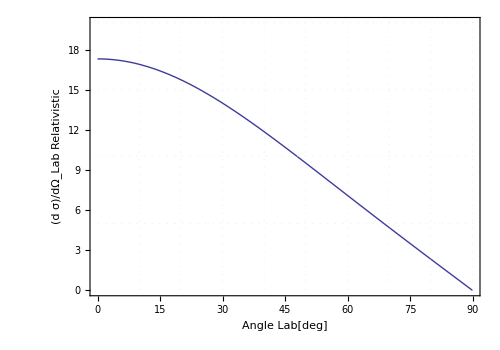

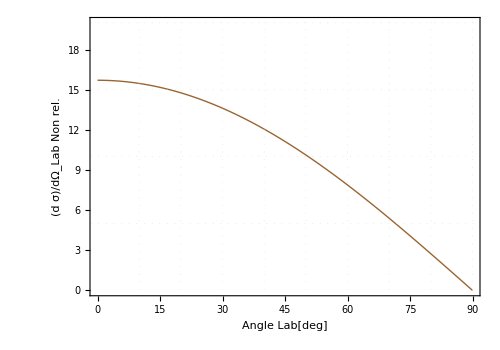

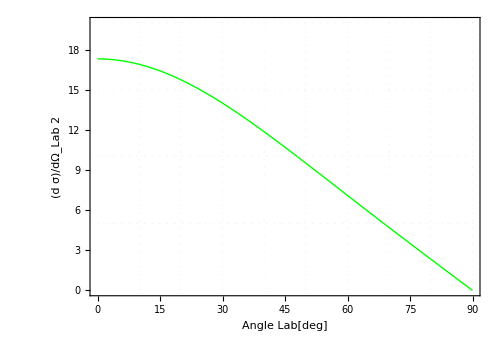

```mathematica
(* For PP elastics *)
mp=938.27203;
c=299792458;
T=260;
P1c[θNN_]:={(√(mp (2 mp+T)))/(√2),√((mp T)/2) Sin[θNN],√((mp T)/2) Cos[θNN]}
g1=ParametricPlot[{ArcTan[√(T (2 mp+T))Cos[θcc/2 °]^2,(√((mp T)/2) Sin[θcc °])] 180/π,3.8Jaco[P1c[θcc °],(√(2 mp T+T^2))/(T+2 mp)]},{θcc,0,180},PlotRange->{{0,90},{0,20}},AspectRatio-> 0.7,Frame-> True, FrameLabel->{"Angle Lab[deg]","(d σ)/dΩ_Lab Relativistic"},GridLines-> {Table[10 i,{i,1,18}],Table[5 i,{i,1,5}]},GridLinesStyle->Directive[Dotted],ImageSize->500]
g2=ParametricPlot[{ArcTan[√(T (2 mp+T))Cos[θcc/2 °]^2,(√((mp T)/2) Sin[θcc °])] 180/π,3.8JacoNonRel[P1c[θcc °],(√(2 mp T+T^2))/(T+2 mp)]},{θcc,0,180},PlotRange->{{0,90},{0,20}},AspectRatio-> 0.7,Frame-> True, FrameLabel->{"Angle Lab[deg]","(d σ)/dΩ_Lab Non rel."},GridLines-> {Table[10 i,{i,1,18}],Table[5 i,{i,1,5}]},GridLinesStyle->Directive[Dotted],ImageSize->500,PlotStyle->Brown]
g3=ParametricPlot[{ArcTan[√(T (2 mp+T))Cos[θcc/2 °]^2,(√((mp T)/2) Sin[θcc °])] 180/π,3.8Jaco2[P1c[θcc °],(√(2 mp T+T^2))/(T+2 mp)]},{θcc,0,180},PlotRange->{{0,90},{0,20}},AspectRatio-> 0.7,Frame-> True, FrameLabel->{"Angle Lab[deg]","(d σ)/dΩ_Lab 2"},GridLines-> {Table[10 i,{i,1,18}],Table[5 i,{i,1,5}]},GridLinesStyle->Directive[Dotted],ImageSize->500,PlotStyle->Green]
```

```mathematica
Dsc260Dist=Interpolation[{{5.00,16.62},{10.00,16.16},{15.00,15.98},{20.00,15.57},{25.00,14.93},{30.00,14.01},{35.00,12.88},{40.00,11.70},{45.00,10.55},{50.00,9.431},{55.00,8.302},{60.00,7.112},{65.00,5.865},{70.00,4.616},{75.00,3.401},{80.00,2.218},{85.00,1.22},{90.00,0}}];
```

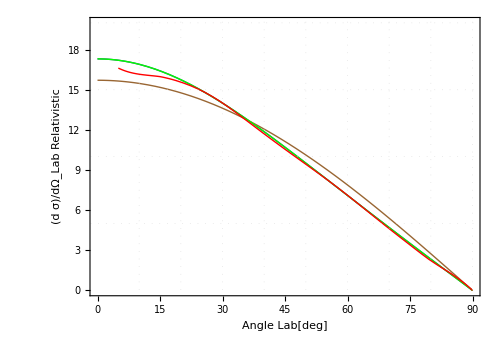

```mathematica
Show[
g1,g2,g3,
Plot[Dsc260Dist[x],{x,5,90},PlotStyle->Red]
]
```

## Systematic method

```mathematica
(* [1977]Scattering kinematics-Transformation of differential cross sections bwteen 2 moving frames*)
```

```mathematica
(*the treansformation equations between A frame to C frame are*)
pc Cos[θc] == γ β Ea + γ pa Cos[θa];
pc Sin[θc]Cos[ϕc] == pa Sin[θa] Cos[ϕa];
pc Sin[θc]Sin[ϕc] == pa Sin[θa] Sin[ϕa];

(*the Jacobian = Jij = (∂Xc)/(∂Xa)*)
```

```mathematica
(* for the J(pc, Ωc|pa, Ωa) , from c frame to a frame *)
(* Apply the ∂/(∂pa),∂/(∂Cos[θa])and ∂/(∂ϕa) operator on each equation *)
```

```mathematica
KK={
{Cos[θc], pc},
{Sin[θc] , - pc Cot[θc]}};
HH = {
{γ β pa/Ea+γ Cos[θa], γ pa},
{Sin[θa], -pa Cot[θa] }};
J=Inverse[KK].HH//FullSimplify
Det[J]//Simplify
Simplify[Det[J], γ(Ea+pa β Cos[θa])==Ec]
```

{{(γ (pa β+Ea Cos[θa]) Cos[θc])/Ea+Sin[θa] Sin[θc],pa (γ Cos[θc]-Cot[θa] Sin[θc])},{(Sin[θc] (-Ea Cos[θc] Sin[θa]+γ (pa β+Ea Cos[θa]) Sin[θc]))/(Ea pc),(pa Sin[θc] (Cos[θc] Cot[θa]+γ Sin[θc]))/pc}}

(pa γ (Ea+pa β Cos[θa]) Csc[θa] Sin[θc])/(Ea pc)

(pa γ (Ea+pa β Cos[θa]) Csc[θa] Sin[θc])/(Ea pc)

```mathematica
KK={
{Cos[θc], pc, 0},
{Sin[θc] Cos[ϕc], - pc Cot[θc] Cos[ϕc], - pc Sin[θc] Sin[ϕc]},
{Sin[θc] Sin[ϕc], - pc Cot[θc] Sin[ϕc],  pc Sin[θc] Cos[ϕc]}};
HH = {
{γ β pa/Ea+γ Cos[θa], γ pa, 0},
{Sin[θa]Cos[ϕa], -pa Cot[θa] Cos[ϕa],-pa Sin[θa] Sin[ϕa]},
{Sin[θa]Sin[ϕa], -pa Cot[θa] Sin[ϕa], pa Sin[θa] Cos[ϕa]}};
J=Inverse[KK].HH//FullSimplify
Det[J]//Simplify
Simplify[Det[J], γ(Ea+pa β Cos[θa])==Ec]
```

{{(γ (pa β+Ea Cos[θa]) Cos[θc])/Ea+Cos[ϕa-ϕc] Sin[θa] Sin[θc],pa (γ Cos[θc]-Cos[ϕa-ϕc] Cot[θa] Sin[θc]),-pa Sin[θa] Sin[θc] Sin[ϕa-ϕc]},{(Sin[θc] (-Ea Cos[θc] Cos[ϕa-ϕc] Sin[θa]+γ (pa β+Ea Cos[θa]) Sin[θc]))/(Ea pc),(pa Sin[θc] (Cos[θc] Cos[ϕa-ϕc] Cot[θa]+γ Sin[θc]))/pc,(pa Sin[θa] Sin[2 θc] Sin[ϕa-ϕc])/(2 pc)},{(Csc[θc] Sin[θa] Sin[ϕa-ϕc])/pc,-(pa Cot[θa] Csc[θc] Sin[ϕa-ϕc])/pc,(pa Cos[ϕa-ϕc] Csc[θc] Sin[θa])/pc}}

(pa^2 γ (Ea+pa β Cos[θa]))/(Ea pc^2)

(Ec pa^2)/(Ea pc^2)

```mathematica
kk={
{Cos[θa], pa, 0},
{Sin[θa] Cos[ϕa], - pa Cot[θa] Cos[ϕa], - pa Sin[θa] Sin[ϕa]},
{Sin[θa] Sin[ϕa], - pa Cot[θa] Sin[ϕa],  pa Sin[θa] Cos[ϕa]}};
hh = {
{-γ β pc/Ec+γ Cos[θc], γ pc, 0},
{Sin[θc]Cos[ϕc], -pc Cot[θc] Cos[ϕc],-pc Sin[θc] Sin[ϕc]},
{Sin[θc]Sin[ϕc], -pc Cot[θc] Sin[ϕc], pc Sin[θc] Cos[ϕc]}};
j=Inverse[kk].hh//FullSimplify
Det[j]//Simplify
Simplify[Det[j], γ(Ec-pc β Cos[θc])==Ea]
```

{{(γ Cos[θa] (-pc β+Ec Cos[θc]))/Ec+Cos[ϕa-ϕc] Sin[θa] Sin[θc],pc (γ Cos[θa]-Cos[ϕa-ϕc] Cot[θc] Sin[θa]),pc Sin[θa] Sin[θc] Sin[ϕa-ϕc]},{-(Sin[θa] (γ (pc β-Ec Cos[θc]) Sin[θa]+Ec Cos[θa] Cos[ϕa-ϕc] Sin[θc]))/(Ec pa),(pc Sin[θa] (Cos[θa] Cos[ϕa-ϕc] Cot[θc]+γ Sin[θa]))/pa,-(pc Sin[2 θa] Sin[θc] Sin[ϕa-ϕc])/(2 pa)},{-(Csc[θa] Sin[θc] Sin[ϕa-ϕc])/pa,(pc Cot[θc] Csc[θa] Sin[ϕa-ϕc])/pa,(pc Cos[ϕa-ϕc] Csc[θa] Sin[θc])/pa}}

(pc^2 γ (Ec-pc β Cos[θc]))/(Ec pa^2)

(Ea pc^2)/(Ec pa^2)

```mathematica
J.j//Simplify//MatrixForm
Simplify[Det[J]Det[j],{ γ(Ea+pa β Cos[θa])==Ec, γ(Ec-pc β Cos[θc])==Ea}]
```

((-2 pc β γ^2 (Ea+pa β Cos[θa]) Cos[θc]+Ec (Ea (-1+γ^2)+2 pa β γ^2 Cos[θa]) Cos[θc]^2+Ec (Ea+Ea γ^2-Ea (-1+γ^2) Sin[θc]^2+pa β γ Cos[ϕa] Cos[ϕc] Sin[θa] Sin[2 θc]+pa β γ Sin[θa] Sin[2 θc] Sin[ϕa] Sin[ϕc]))/(2 Ea Ec) | (pc Cos[θc] (-Ea+Ea γ^2+pa β γ^2 Cos[θa]-pa β γ Cos[ϕa] Cos[ϕc] Cot[θc] Sin[θa]-pa β γ Cot[θc] Sin[θa] Sin[ϕa] Sin[ϕc]))/Ea | (pa pc β γ Sin[θa] Sin[2 θc] Sin[ϕa-ϕc])/(2 Ea)
(Sin[θc]^2 (Ea Ec (-1+γ^2) Cos[θc]-pa β γ^2 Cos[θa] (pc β-Ec Cos[θc])+β γ (-Ea pc γ+Ec pa Cos[ϕa] Cos[ϕc] Sin[θa] Sin[θc]+Ec pa Sin[θa] Sin[θc] Sin[ϕa] Sin[ϕc])))/(Ea Ec pc) | (Ea+Ea γ^2-Ea (-1+γ^2) Cos[θc]^2+(Ea (-1+γ^2)+2 pa β γ^2 Cos[θa]) Sin[θc]^2-pa β γ Cos[ϕa-ϕc] Sin[θa] Sin[2 θc])/(2 Ea) | (pa β γ Sin[θa] Sin[θc]^3 Sin[ϕa-ϕc])/Ea
0 | 0 | 1)

1

```mathematica
(* for E, Ω *)
KK={
{Ec/pc pa/Ea Cos[θc],pa/Ea pc, 0},
{Ec/pc Sin[θc] Cos[ϕc], - pc Cot[θc] Cos[ϕc], - pc Sin[θc] Sin[ϕc]},
{Ec/pc Sin[θc] Sin[ϕc], - pc Cot[θc] Sin[ϕc],  pc Sin[θc] Cos[ϕc]}};
HH = {
{γ β pa/Ea+γ Cos[θa], γ pa, 0},
{Sin[θa]Cos[ϕa], -pa Cot[θa] Cos[ϕa],-pa Sin[θa] Sin[ϕa]},
{Sin[θa]Sin[ϕa], -pa Cot[θa] Sin[ϕa], pa Sin[θa] Cos[ϕa]}};
J=Inverse[KK].HH//FullSimplify
Det[J]//Simplify
```

{{(pc (γ (pa β+Ea Cos[θa]) Cos[θc]+pa Cos[ϕa-ϕc] Sin[θa] Sin[θc]))/(Ec pa),(pc (Ea γ Cos[θc]-pa Cos[ϕa-ϕc] Cot[θa] Sin[θc]))/Ec,-(pa pc Sin[θa] Sin[θc] Sin[ϕa-ϕc])/Ec},{(Sin[θc] (-pa Cos[θc] Cos[ϕa-ϕc] Sin[θa]+γ (pa β+Ea Cos[θa]) Sin[θc]))/(pa pc),(Sin[θc] (pa Cos[θc] Cos[ϕa-ϕc] Cot[θa]+Ea γ Sin[θc]))/pc,(pa Sin[θa] Sin[2 θc] Sin[ϕa-ϕc])/(2 pc)},{(Csc[θc] Sin[θa] Sin[ϕa-ϕc])/pc,-(pa Cot[θa] Csc[θc] Sin[ϕa-ϕc])/pc,(pa Cos[ϕa-ϕc] Csc[θc] Sin[θa])/pc}}

(pa γ (Ea+pa β Cos[θa]))/(Ec pc)